# Gaussian quadrature

```mathematica
LGAUSS[Nr_]:=Module[{root,xi,DP,wg,x},
root= Sort[Solve[LegendreP[Nr, x] == 0, {x}] // N];
xi=x/.root;
DP=Evaluate[D[LegendreP[Nr,x],x]]/.root;
wg=2/((1-xi^2)DP^2);
Table[{xi[[i]],wg[[i]]},{i,1,Nr}]
]
GaussianIntegrate[f_Symbol,a_,b_,nGauss_]:=Module[
{func,xwlist,temp},
func[x_]:=f[x];
xwlist=Transpose[LGAUSS[nGauss]];
(*Print[ListPlot[Transpose[Join[{xwlist[[1]]},{func[(b-a)/2 xwlist[[1]]+(b+a)/2]}]]]];*)
(*(b-a)/2 Total[xwlist[[2]]func[(b-a)/2 xwlist[[1]]+(b+a)/2]];*)
(b-a)/2 Sum[xwlist[[2,i]]func[(b-a)/2 xwlist[[1,i]]+(b+a)/2],{i,1,nGauss}]

]
```

```mathematica
G[x_,g1_,g2_]:=x^(3/2)+g1/(1+g2 x)
test[x_,g1_,g2_]:=G[x,g1,g2]/(x^2+(G[x,g1,g2])^2)
xRange={0,10};
sol=Table[
xwlist=Transpose[LGAUSS[16]];
{g1,g2,
10/2 Sum[xwlist[[2,i]]test[10/2 xwlist[[1,i]]+10/2,g1,g2],{i,1,16}]
},{g1,2.7-0.3,2.7+0.3,0.02},{g2,1.3-0.3,1.3+0.3,0.02}];
```

```mathematica
Manipulate[
Plot[test[x,g1,g2],{x,0,10}],
{{g1,2.7},2.4,3},
{{g2,1.3},1,1.6}]
```

```mathematica
TableForm[Round[sol,0.01],TableDepth->2]
```

{2.4,1.,1.33} | {2.4,1.02,1.33} | {2.4,1.04,1.33} | {2.4,1.06,1.34} | {2.4,1.08,1.34} | {2.4,1.1,1.34} | {2.4,1.12,1.34} | {2.4,1.14,1.35} | {2.4,1.16,1.35} | {2.4,1.18,1.35} | {2.4,1.2,1.35} | {2.4,1.22,1.36} | {2.4,1.24,1.36} | {2.4,1.26,1.36} | {2.4,1.28,1.36} | {2.4,1.3,1.37} | {2.4,1.32,1.37} | {2.4,1.34,1.37} | {2.4,1.36,1.37} | {2.4,1.38,1.38} | {2.4,1.4,1.38} | {2.4,1.42,1.38} | {2.4,1.44,1.38} | {2.4,1.46,1.38} | {2.4,1.48,1.39} | {2.4,1.5,1.39} | {2.4,1.52,1.39} | {2.4,1.54,1.39} | {2.4,1.56,1.39} | {2.4,1.58,1.4} | {2.4,1.6,1.4}
{2.42,1.,1.32} | {2.42,1.02,1.33} | {2.42,1.04,1.33} | {2.42,1.06,1.33} | {2.42,1.08,1.34} | {2.42,1.1,1.34} | {2.42,1.12,1.34} | {2.42,1.14,1.34} | {2.42,1.16,1.35} | {2.42,1.18,1.35} | {2.42,1.2,1.35} | {2.42,1.22,1.35} | {2.42,1.24,1.36} | {2.42,1.26,1.36} | {2.42,1.28,1.36} | {2.42,1.3,1.36} | {2.42,1.32,1.37} | {2.42,1.34,1.37} | {2.42,1.36,1.37} | {2.42,1.38,1.37} | {2.42,1.4,1.37} | {2.42,1.42,1.38} | {2.42,1.44,1.38} | {2.42,1.46,1.38} | {2.42,1.48,1.38} | {2.42,1.5,1.39} | {2.42,1.52,1.39} | {2.42,1.54,1.39} | {2.42,1.56,1.39} | {2.42,1.58,1.39} | {2.42,1.6,1.4}
{2.44,1.,1.32} | {2.44,1.02,1.32} | {2.44,1.04,1.33} | {2.44,1.06,1.33} | {2.44,1.08,1.33} | {2.44,1.1,1.33} | {2.44,1.12,1.34} | {2.44,1.14,1.34} | {2.44,1.16,1.34} | {2.44,1.18,1.34} | {2.44,1.2,1.35} | {2.44,1.22,1.35} | {2.44,1.24,1.35} | {2.44,1.26,1.35} | {2.44,1.28,1.36} | {2.44,1.3,1.36} | {2.44,1.32,1.36} | {2.44,1.34,1.36} | {2.44,1.36,1.37} | {2.44,1.38,1.37} | {2.44,1.4,1.37} | {2.44,1.42,1.37} | {2.44,1.44,1.38} | {2.44,1.46,1.38} | {2.44,1.48,1.38} | {2.44,1.5,1.38} | {2.44,1.52,1.38} | {2.44,1.54,1.39} | {2.44,1.56,1.39} | {2.44,1.58,1.39} | {2.44,1.6,1.39}
{2.46,1.,1.32} | {2.46,1.02,1.32} | {2.46,1.04,1.32} | {2.46,1.06,1.33} | {2.46,1.08,1.33} | {2.46,1.1,1.33} | {2.46,1.12,1.33} | {2.46,1.14,1.34} | {2.46,1.16,1.34} | {2.46,1.18,1.34} | {2.46,1.2,1.34} | {2.46,1.22,1.35} | {2.46,1.24,1.35} | {2.46,1.26,1.35} | {2.46,1.28,1.35} | {2.46,1.3,1.36} | {2.46,1.32,1.36} | {2.46,1.34,1.36} | {2.46,1.36,1.36} | {2.46,1.38,1.37} | {2.46,1.4,1.37} | {2.46,1.42,1.37} | {2.46,1.44,1.37} | {2.46,1.46,1.37} | {2.46,1.48,1.38} | {2.46,1.5,1.38} | {2.46,1.52,1.38} | {2.46,1.54,1.38} | {2.46,1.56,1.39} | {2.46,1.58,1.39} | {2.46,1.6,1.39}
{2.48,1.,1.31} | {2.48,1.02,1.32} | {2.48,1.04,1.32} | {2.48,1.06,1.32} | {2.48,1.08,1.33} | {2.48,1.1,1.33} | {2.48,1.12,1.33} | {2.48,1.14,1.33} | {2.48,1.16,1.34} | {2.48,1.18,1.34} | {2.48,1.2,1.34} | {2.48,1.22,1.34} | {2.48,1.24,1.35} | {2.48,1.26,1.35} | {2.48,1.28,1.35} | {2.48,1.3,1.35} | {2.48,1.32,1.36} | {2.48,1.34,1.36} | {2.48,1.36,1.36} | {2.48,1.38,1.36} | {2.48,1.4,1.36} | {2.48,1.42,1.37} | {2.48,1.44,1.37} | {2.48,1.46,1.37} | {2.48,1.48,1.37} | {2.48,1.5,1.38} | {2.48,1.52,1.38} | {2.48,1.54,1.38} | {2.48,1.56,1.38} | {2.48,1.58,1.38} | {2.48,1.6,1.39}
{2.5,1.,1.31} | {2.5,1.02,1.31} | {2.5,1.04,1.32} | {2.5,1.06,1.32} | {2.5,1.08,1.32} | {2.5,1.1,1.32} | {2.5,1.12,1.33} | {2.5,1.14,1.33} | {2.5,1.16,1.33} | {2.5,1.18,1.34} | {2.5,1.2,1.34} | {2.5,1.22,1.34} | {2.5,1.24,1.34} | {2.5,1.26,1.35} | {2.5,1.28,1.35} | {2.5,1.3,1.35} | {2.5,1.32,1.35} | {2.5,1.34,1.35} | {2.5,1.36,1.36} | {2.5,1.38,1.36} | {2.5,1.4,1.36} | {2.5,1.42,1.36} | {2.5,1.44,1.37} | {2.5,1.46,1.37} | {2.5,1.48,1.37} | {2.5,1.5,1.37} | {2.5,1.52,1.37} | {2.5,1.54,1.38} | {2.5,1.56,1.38} | {2.5,1.58,1.38} | {2.5,1.6,1.38}
{2.52,1.,1.31} | {2.52,1.02,1.31} | {2.52,1.04,1.31} | {2.52,1.06,1.32} | {2.52,1.08,1.32} | {2.52,1.1,1.32} | {2.52,1.12,1.32} | {2.52,1.14,1.33} | {2.52,1.16,1.33} | {2.52,1.18,1.33} | {2.52,1.2,1.33} | {2.52,1.22,1.34} | {2.52,1.24,1.34} | {2.52,1.26,1.34} | {2.52,1.28,1.34} | {2.52,1.3,1.35} | {2.52,1.32,1.35} | {2.52,1.34,1.35} | {2.52,1.36,1.35} | {2.52,1.38,1.36} | {2.52,1.4,1.36} | {2.52,1.42,1.36} | {2.52,1.44,1.36} | {2.52,1.46,1.36} | {2.52,1.48,1.37} | {2.52,1.5,1.37} | {2.52,1.52,1.37} | {2.52,1.54,1.37} | {2.52,1.56,1.38} | {2.52,1.58,1.38} | {2.52,1.6,1.38}
{2.54,1.,1.3} | {2.54,1.02,1.31} | {2.54,1.04,1.31} | {2.54,1.06,1.31} | {2.54,1.08,1.32} | {2.54,1.1,1.32} | {2.54,1.12,1.32} | {2.54,1.14,1.32} | {2.54,1.16,1.33} | {2.54,1.18,1.33} | {2.54,1.2,1.33} | {2.54,1.22,1.33} | {2.54,1.24,1.34} | {2.54,1.26,1.34} | {2.54,1.28,1.34} | {2.54,1.3,1.34} | {2.54,1.32,1.35} | {2.54,1.34,1.35} | {2.54,1.36,1.35} | {2.54,1.38,1.35} | {2.54,1.4,1.36} | {2.54,1.42,1.36} | {2.54,1.44,1.36} | {2.54,1.46,1.36} | {2.54,1.48,1.36} | {2.54,1.5,1.37} | {2.54,1.52,1.37} | {2.54,1.54,1.37} | {2.54,1.56,1.37} | {2.54,1.58,1.37} | {2.54,1.6,1.38}
{2.56,1.,1.3} | {2.56,1.02,1.3} | {2.56,1.04,1.31} | {2.56,1.06,1.31} | {2.56,1.08,1.31} | {2.56,1.1,1.32} | {2.56,1.12,1.32} | {2.56,1.14,1.32} | {2.56,1.16,1.32} | {2.56,1.18,1.33} | {2.56,1.2,1.33} | {2.56,1.22,1.33} | {2.56,1.24,1.33} | {2.56,1.26,1.34} | {2.56,1.28,1.34} | {2.56,1.3,1.34} | {2.56,1.32,1.34} | {2.56,1.34,1.35} | {2.56,1.36,1.35} | {2.56,1.38,1.35} | {2.56,1.4,1.35} | {2.56,1.42,1.35} | {2.56,1.44,1.36} | {2.56,1.46,1.36} | {2.56,1.48,1.36} | {2.56,1.5,1.36} | {2.56,1.52,1.37} | {2.56,1.54,1.37} | {2.56,1.56,1.37} | {2.56,1.58,1.37} | {2.56,1.6,1.37}
{2.58,1.,1.3} | {2.58,1.02,1.3} | {2.58,1.04,1.3} | {2.58,1.06,1.31} | {2.58,1.08,1.31} | {2.58,1.1,1.31} | {2.58,1.12,1.31} | {2.58,1.14,1.32} | {2.58,1.16,1.32} | {2.58,1.18,1.32} | {2.58,1.2,1.32} | {2.58,1.22,1.33} | {2.58,1.24,1.33} | {2.58,1.26,1.33} | {2.58,1.28,1.33} | {2.58,1.3,1.34} | {2.58,1.32,1.34} | {2.58,1.34,1.34} | {2.58,1.36,1.34} | {2.58,1.38,1.35} | {2.58,1.4,1.35} | {2.58,1.42,1.35} | {2.58,1.44,1.35} | {2.58,1.46,1.36} | {2.58,1.48,1.36} | {2.58,1.5,1.36} | {2.58,1.52,1.36} | {2.58,1.54,1.36} | {2.58,1.56,1.37} | {2.58,1.58,1.37} | {2.58,1.6,1.37}
{2.6,1.,1.3} | {2.6,1.02,1.3} | {2.6,1.04,1.3} | {2.6,1.06,1.3} | {2.6,1.08,1.31} | {2.6,1.1,1.31} | {2.6,1.12,1.31} | {2.6,1.14,1.31} | {2.6,1.16,1.32} | {2.6,1.18,1.32} | {2.6,1.2,1.32} | {2.6,1.22,1.32} | {2.6,1.24,1.33} | {2.6,1.26,1.33} | {2.6,1.28,1.33} | {2.6,1.3,1.33} | {2.6,1.32,1.34} | {2.6,1.34,1.34} | {2.6,1.36,1.34} | {2.6,1.38,1.34} | {2.6,1.4,1.35} | {2.6,1.42,1.35} | {2.6,1.44,1.35} | {2.6,1.46,1.35} | {2.6,1.48,1.35} | {2.6,1.5,1.36} | {2.6,1.52,1.36} | {2.6,1.54,1.36} | {2.6,1.56,1.36} | {2.6,1.58,1.37} | {2.6,1.6,1.37}
{2.62,1.,1.29} | {2.62,1.02,1.29} | {2.62,1.04,1.3} | {2.62,1.06,1.3} | {2.62,1.08,1.3} | {2.62,1.1,1.31} | {2.62,1.12,1.31} | {2.62,1.14,1.31} | {2.62,1.16,1.31} | {2.62,1.18,1.32} | {2.62,1.2,1.32} | {2.62,1.22,1.32} | {2.62,1.24,1.32} | {2.62,1.26,1.33} | {2.62,1.28,1.33} | {2.62,1.3,1.33} | {2.62,1.32,1.33} | {2.62,1.34,1.34} | {2.62,1.36,1.34} | {2.62,1.38,1.34} | {2.62,1.4,1.34} | {2.62,1.42,1.34} | {2.62,1.44,1.35} | {2.62,1.46,1.35} | {2.62,1.48,1.35} | {2.62,1.5,1.35} | {2.62,1.52,1.36} | {2.62,1.54,1.36} | {2.62,1.56,1.36} | {2.62,1.58,1.36} | {2.62,1.6,1.36}
{2.64,1.,1.29} | {2.64,1.02,1.29} | {2.64,1.04,1.29} | {2.64,1.06,1.3} | {2.64,1.08,1.3} | {2.64,1.1,1.3} | {2.64,1.12,1.31} | {2.64,1.14,1.31} | {2.64,1.16,1.31} | {2.64,1.18,1.31} | {2.64,1.2,1.32} | {2.64,1.22,1.32} | {2.64,1.24,1.32} | {2.64,1.26,1.32} | {2.64,1.28,1.33} | {2.64,1.3,1.33} | {2.64,1.32,1.33} | {2.64,1.34,1.33} | {2.64,1.36,1.34} | {2.64,1.38,1.34} | {2.64,1.4,1.34} | {2.64,1.42,1.34} | {2.64,1.44,1.34} | {2.64,1.46,1.35} | {2.64,1.48,1.35} | {2.64,1.5,1.35} | {2.64,1.52,1.35} | {2.64,1.54,1.36} | {2.64,1.56,1.36} | {2.64,1.58,1.36} | {2.64,1.6,1.36}
{2.66,1.,1.29} | {2.66,1.02,1.29} | {2.66,1.04,1.29} | {2.66,1.06,1.29} | {2.66,1.08,1.3} | {2.66,1.1,1.3} | {2.66,1.12,1.3} | {2.66,1.14,1.31} | {2.66,1.16,1.31} | {2.66,1.18,1.31} | {2.66,1.2,1.31} | {2.66,1.22,1.32} | {2.66,1.24,1.32} | {2.66,1.26,1.32} | {2.66,1.28,1.32} | {2.66,1.3,1.33} | {2.66,1.32,1.33} | {2.66,1.34,1.33} | {2.66,1.36,1.33} | {2.66,1.38,1.33} | {2.66,1.4,1.34} | {2.66,1.42,1.34} | {2.66,1.44,1.34} | {2.66,1.46,1.34} | {2.66,1.48,1.35} | {2.66,1.5,1.35} | {2.66,1.52,1.35} | {2.66,1.54,1.35} | {2.66,1.56,1.35} | {2.66,1.58,1.36} | {2.66,1.6,1.36}
{2.68,1.,1.28} | {2.68,1.02,1.29} | {2.68,1.04,1.29} | {2.68,1.06,1.29} | {2.68,1.08,1.29} | {2.68,1.1,1.3} | {2.68,1.12,1.3} | {2.68,1.14,1.3} | {2.68,1.16,1.3} | {2.68,1.18,1.31} | {2.68,1.2,1.31} | {2.68,1.22,1.31} | {2.68,1.24,1.31} | {2.68,1.26,1.32} | {2.68,1.28,1.32} | {2.68,1.3,1.32} | {2.68,1.32,1.32} | {2.68,1.34,1.33} | {2.68,1.36,1.33} | {2.68,1.38,1.33} | {2.68,1.4,1.33} | {2.68,1.42,1.34} | {2.68,1.44,1.34} | {2.68,1.46,1.34} | {2.68,1.48,1.34} | {2.68,1.5,1.34} | {2.68,1.52,1.35} | {2.68,1.54,1.35} | {2.68,1.56,1.35} | {2.68,1.58,1.35} | {2.68,1.6,1.36}
{2.7,1.,1.28} | {2.7,1.02,1.28} | {2.7,1.04,1.29} | {2.7,1.06,1.29} | {2.7,1.08,1.29} | {2.7,1.1,1.29} | {2.7,1.12,1.3} | {2.7,1.14,1.3} | {2.7,1.16,1.3} | {2.7,1.18,1.3} | {2.7,1.2,1.31} | {2.7,1.22,1.31} | {2.7,1.24,1.31} | {2.7,1.26,1.31} | {2.7,1.28,1.32} | {2.7,1.3,1.32} | {2.7,1.32,1.32} | {2.7,1.34,1.32} | {2.7,1.36,1.33} | {2.7,1.38,1.33} | {2.7,1.4,1.33} | {2.7,1.42,1.33} | {2.7,1.44,1.34} | {2.7,1.46,1.34} | {2.7,1.48,1.34} | {2.7,1.5,1.34} | {2.7,1.52,1.34} | {2.7,1.54,1.35} | {2.7,1.56,1.35} | {2.7,1.58,1.35} | {2.7,1.6,1.35}
{2.72,1.,1.28} | {2.72,1.02,1.28} | {2.72,1.04,1.28} | {2.72,1.06,1.29} | {2.72,1.08,1.29} | {2.72,1.1,1.29} | {2.72,1.12,1.29} | {2.72,1.14,1.3} | {2.72,1.16,1.3} | {2.72,1.18,1.3} | {2.72,1.2,1.3} | {2.72,1.22,1.31} | {2.72,1.24,1.31} | {2.72,1.26,1.31} | {2.72,1.28,1.31} | {2.72,1.3,1.32} | {2.72,1.32,1.32} | {2.72,1.34,1.32} | {2.72,1.36,1.32} | {2.72,1.38,1.33} | {2.72,1.4,1.33} | {2.72,1.42,1.33} | {2.72,1.44,1.33} | {2.72,1.46,1.33} | {2.72,1.48,1.34} | {2.72,1.5,1.34} | {2.72,1.52,1.34} | {2.72,1.54,1.34} | {2.72,1.56,1.35} | {2.72,1.58,1.35} | {2.72,1.6,1.35}
{2.74,1.,1.27} | {2.74,1.02,1.28} | {2.74,1.04,1.28} | {2.74,1.06,1.28} | {2.74,1.08,1.29} | {2.74,1.1,1.29} | {2.74,1.12,1.29} | {2.74,1.14,1.29} | {2.74,1.16,1.3} | {2.74,1.18,1.3} | {2.74,1.2,1.3} | {2.74,1.22,1.3} | {2.74,1.24,1.31} | {2.74,1.26,1.31} | {2.74,1.28,1.31} | {2.74,1.3,1.31} | {2.74,1.32,1.32} | {2.74,1.34,1.32} | {2.74,1.36,1.32} | {2.74,1.38,1.32} | {2.74,1.4,1.33} | {2.74,1.42,1.33} | {2.74,1.44,1.33} | {2.74,1.46,1.33} | {2.74,1.48,1.33} | {2.74,1.5,1.34} | {2.74,1.52,1.34} | {2.74,1.54,1.34} | {2.74,1.56,1.34} | {2.74,1.58,1.34} | {2.74,1.6,1.35}
{2.76,1.,1.27} | {2.76,1.02,1.27} | {2.76,1.04,1.28} | {2.76,1.06,1.28} | {2.76,1.08,1.28} | {2.76,1.1,1.29} | {2.76,1.12,1.29} | {2.76,1.14,1.29} | {2.76,1.16,1.29} | {2.76,1.18,1.3} | {2.76,1.2,1.3} | {2.76,1.22,1.3} | {2.76,1.24,1.3} | {2.76,1.26,1.31} | {2.76,1.28,1.31} | {2.76,1.3,1.31} | {2.76,1.32,1.31} | {2.76,1.34,1.32} | {2.76,1.36,1.32} | {2.76,1.38,1.32} | {2.76,1.4,1.32} | {2.76,1.42,1.32} | {2.76,1.44,1.33} | {2.76,1.46,1.33} | {2.76,1.48,1.33} | {2.76,1.5,1.33} | {2.76,1.52,1.34} | {2.76,1.54,1.34} | {2.76,1.56,1.34} | {2.76,1.58,1.34} | {2.76,1.6,1.34}
{2.78,1.,1.27} | {2.78,1.02,1.27} | {2.78,1.04,1.27} | {2.78,1.06,1.28} | {2.78,1.08,1.28} | {2.78,1.1,1.28} | {2.78,1.12,1.28} | {2.78,1.14,1.29} | {2.78,1.16,1.29} | {2.78,1.18,1.29} | {2.78,1.2,1.3} | {2.78,1.22,1.3} | {2.78,1.24,1.3} | {2.78,1.26,1.3} | {2.78,1.28,1.31} | {2.78,1.3,1.31} | {2.78,1.32,1.31} | {2.78,1.34,1.31} | {2.78,1.36,1.31} | {2.78,1.38,1.32} | {2.78,1.4,1.32} | {2.78,1.42,1.32} | {2.78,1.44,1.32} | {2.78,1.46,1.33} | {2.78,1.48,1.33} | {2.78,1.5,1.33} | {2.78,1.52,1.33} | {2.78,1.54,1.33} | {2.78,1.56,1.34} | {2.78,1.58,1.34} | {2.78,1.6,1.34}
{2.8,1.,1.27} | {2.8,1.02,1.27} | {2.8,1.04,1.27} | {2.8,1.06,1.27} | {2.8,1.08,1.28} | {2.8,1.1,1.28} | {2.8,1.12,1.28} | {2.8,1.14,1.28} | {2.8,1.16,1.29} | {2.8,1.18,1.29} | {2.8,1.2,1.29} | {2.8,1.22,1.29} | {2.8,1.24,1.3} | {2.8,1.26,1.3} | {2.8,1.28,1.3} | {2.8,1.3,1.3} | {2.8,1.32,1.31} | {2.8,1.34,1.31} | {2.8,1.36,1.31} | {2.8,1.38,1.31} | {2.8,1.4,1.32} | {2.8,1.42,1.32} | {2.8,1.44,1.32} | {2.8,1.46,1.32} | {2.8,1.48,1.33} | {2.8,1.5,1.33} | {2.8,1.52,1.33} | {2.8,1.54,1.33} | {2.8,1.56,1.33} | {2.8,1.58,1.34} | {2.8,1.6,1.34}
{2.82,1.,1.26} | {2.82,1.02,1.27} | {2.82,1.04,1.27} | {2.82,1.06,1.27} | {2.82,1.08,1.27} | {2.82,1.1,1.28} | {2.82,1.12,1.28} | {2.82,1.14,1.28} | {2.82,1.16,1.28} | {2.82,1.18,1.29} | {2.82,1.2,1.29} | {2.82,1.22,1.29} | {2.82,1.24,1.29} | {2.82,1.26,1.3} | {2.82,1.28,1.3} | {2.82,1.3,1.3} | {2.82,1.32,1.3} | {2.82,1.34,1.31} | {2.82,1.36,1.31} | {2.82,1.38,1.31} | {2.82,1.4,1.31} | {2.82,1.42,1.32} | {2.82,1.44,1.32} | {2.82,1.46,1.32} | {2.82,1.48,1.32} | {2.82,1.5,1.32} | {2.82,1.52,1.33} | {2.82,1.54,1.33} | {2.82,1.56,1.33} | {2.82,1.58,1.33} | {2.82,1.6,1.34}
{2.84,1.,1.26} | {2.84,1.02,1.26} | {2.84,1.04,1.27} | {2.84,1.06,1.27} | {2.84,1.08,1.27} | {2.84,1.1,1.27} | {2.84,1.12,1.28} | {2.84,1.14,1.28} | {2.84,1.16,1.28} | {2.84,1.18,1.28} | {2.84,1.2,1.29} | {2.84,1.22,1.29} | {2.84,1.24,1.29} | {2.84,1.26,1.29} | {2.84,1.28,1.3} | {2.84,1.3,1.3} | {2.84,1.32,1.3} | {2.84,1.34,1.3} | {2.84,1.36,1.31} | {2.84,1.38,1.31} | {2.84,1.4,1.31} | {2.84,1.42,1.31} | {2.84,1.44,1.32} | {2.84,1.46,1.32} | {2.84,1.48,1.32} | {2.84,1.5,1.32} | {2.84,1.52,1.32} | {2.84,1.54,1.33} | {2.84,1.56,1.33} | {2.84,1.58,1.33} | {2.84,1.6,1.33}
{2.86,1.,1.26} | {2.86,1.02,1.26} | {2.86,1.04,1.26} | {2.86,1.06,1.27} | {2.86,1.08,1.27} | {2.86,1.1,1.27} | {2.86,1.12,1.27} | {2.86,1.14,1.28} | {2.86,1.16,1.28} | {2.86,1.18,1.28} | {2.86,1.2,1.28} | {2.86,1.22,1.29} | {2.86,1.24,1.29} | {2.86,1.26,1.29} | {2.86,1.28,1.29} | {2.86,1.3,1.3} | {2.86,1.32,1.3} | {2.86,1.34,1.3} | {2.86,1.36,1.3} | {2.86,1.38,1.31} | {2.86,1.4,1.31} | {2.86,1.42,1.31} | {2.86,1.44,1.31} | {2.86,1.46,1.32} | {2.86,1.48,1.32} | {2.86,1.5,1.32} | {2.86,1.52,1.32} | {2.86,1.54,1.32} | {2.86,1.56,1.33} | {2.86,1.58,1.33} | {2.86,1.6,1.33}
{2.88,1.,1.25} | {2.88,1.02,1.26} | {2.88,1.04,1.26} | {2.88,1.06,1.26} | {2.88,1.08,1.27} | {2.88,1.1,1.27} | {2.88,1.12,1.27} | {2.88,1.14,1.27} | {2.88,1.16,1.28} | {2.88,1.18,1.28} | {2.88,1.2,1.28} | {2.88,1.22,1.28} | {2.88,1.24,1.29} | {2.88,1.26,1.29} | {2.88,1.28,1.29} | {2.88,1.3,1.29} | {2.88,1.32,1.3} | {2.88,1.34,1.3} | {2.88,1.36,1.3} | {2.88,1.38,1.3} | {2.88,1.4,1.31} | {2.88,1.42,1.31} | {2.88,1.44,1.31} | {2.88,1.46,1.31} | {2.88,1.48,1.31} | {2.88,1.5,1.32} | {2.88,1.52,1.32} | {2.88,1.54,1.32} | {2.88,1.56,1.32} | {2.88,1.58,1.33} | {2.88,1.6,1.33}
{2.9,1.,1.25} | {2.9,1.02,1.25} | {2.9,1.04,1.26} | {2.9,1.06,1.26} | {2.9,1.08,1.26} | {2.9,1.1,1.27} | {2.9,1.12,1.27} | {2.9,1.14,1.27} | {2.9,1.16,1.27} | {2.9,1.18,1.28} | {2.9,1.2,1.28} | {2.9,1.22,1.28} | {2.9,1.24,1.28} | {2.9,1.26,1.29} | {2.9,1.28,1.29} | {2.9,1.3,1.29} | {2.9,1.32,1.29} | {2.9,1.34,1.3} | {2.9,1.36,1.3} | {2.9,1.38,1.3} | {2.9,1.4,1.3} | {2.9,1.42,1.31} | {2.9,1.44,1.31} | {2.9,1.46,1.31} | {2.9,1.48,1.31} | {2.9,1.5,1.31} | {2.9,1.52,1.32} | {2.9,1.54,1.32} | {2.9,1.56,1.32} | {2.9,1.58,1.32} | {2.9,1.6,1.32}
{2.92,1.,1.25} | {2.92,1.02,1.25} | {2.92,1.04,1.25} | {2.92,1.06,1.26} | {2.92,1.08,1.26} | {2.92,1.1,1.26} | {2.92,1.12,1.27} | {2.92,1.14,1.27} | {2.92,1.16,1.27} | {2.92,1.18,1.27} | {2.92,1.2,1.28} | {2.92,1.22,1.28} | {2.92,1.24,1.28} | {2.92,1.26,1.28} | {2.92,1.28,1.29} | {2.92,1.3,1.29} | {2.92,1.32,1.29} | {2.92,1.34,1.29} | {2.92,1.36,1.3} | {2.92,1.38,1.3} | {2.92,1.4,1.3} | {2.92,1.42,1.3} | {2.92,1.44,1.3} | {2.92,1.46,1.31} | {2.92,1.48,1.31} | {2.92,1.5,1.31} | {2.92,1.52,1.31} | {2.92,1.54,1.32} | {2.92,1.56,1.32} | {2.92,1.58,1.32} | {2.92,1.6,1.32}
{2.94,1.,1.25} | {2.94,1.02,1.25} | {2.94,1.04,1.25} | {2.94,1.06,1.25} | {2.94,1.08,1.26} | {2.94,1.1,1.26} | {2.94,1.12,1.26} | {2.94,1.14,1.27} | {2.94,1.16,1.27} | {2.94,1.18,1.27} | {2.94,1.2,1.27} | {2.94,1.22,1.28} | {2.94,1.24,1.28} | {2.94,1.26,1.28} | {2.94,1.28,1.28} | {2.94,1.3,1.29} | {2.94,1.32,1.29} | {2.94,1.34,1.29} | {2.94,1.36,1.29} | {2.94,1.38,1.3} | {2.94,1.4,1.3} | {2.94,1.42,1.3} | {2.94,1.44,1.3} | {2.94,1.46,1.3} | {2.94,1.48,1.31} | {2.94,1.5,1.31} | {2.94,1.52,1.31} | {2.94,1.54,1.31} | {2.94,1.56,1.32} | {2.94,1.58,1.32} | {2.94,1.6,1.32}
{2.96,1.,1.24} | {2.96,1.02,1.25} | {2.96,1.04,1.25} | {2.96,1.06,1.25} | {2.96,1.08,1.25} | {2.96,1.1,1.26} | {2.96,1.12,1.26} | {2.96,1.14,1.26} | {2.96,1.16,1.27} | {2.96,1.18,1.27} | {2.96,1.2,1.27} | {2.96,1.22,1.27} | {2.96,1.24,1.28} | {2.96,1.26,1.28} | {2.96,1.28,1.28} | {2.96,1.3,1.28} | {2.96,1.32,1.29} | {2.96,1.34,1.29} | {2.96,1.36,1.29} | {2.96,1.38,1.29} | {2.96,1.4,1.29} | {2.96,1.42,1.3} | {2.96,1.44,1.3} | {2.96,1.46,1.3} | {2.96,1.48,1.3} | {2.96,1.5,1.31} | {2.96,1.52,1.31} | {2.96,1.54,1.31} | {2.96,1.56,1.31} | {2.96,1.58,1.31} | {2.96,1.6,1.32}
{2.98,1.,1.24} | {2.98,1.02,1.24} | {2.98,1.04,1.25} | {2.98,1.06,1.25} | {2.98,1.08,1.25} | {2.98,1.1,1.25} | {2.98,1.12,1.26} | {2.98,1.14,1.26} | {2.98,1.16,1.26} | {2.98,1.18,1.27} | {2.98,1.2,1.27} | {2.98,1.22,1.27} | {2.98,1.24,1.27} | {2.98,1.26,1.28} | {2.98,1.28,1.28} | {2.98,1.3,1.28} | {2.98,1.32,1.28} | {2.98,1.34,1.29} | {2.98,1.36,1.29} | {2.98,1.38,1.29} | {2.98,1.4,1.29} | {2.98,1.42,1.29} | {2.98,1.44,1.3} | {2.98,1.46,1.3} | {2.98,1.48,1.3} | {2.98,1.5,1.3} | {2.98,1.52,1.31} | {2.98,1.54,1.31} | {2.98,1.56,1.31} | {2.98,1.58,1.31} | {2.98,1.6,1.31}
{3.,1.,1.24} | {3.,1.02,1.24} | {3.,1.04,1.24} | {3.,1.06,1.25} | {3.,1.08,1.25} | {3.,1.1,1.25} | {3.,1.12,1.25} | {3.,1.14,1.26} | {3.,1.16,1.26} | {3.,1.18,1.26} | {3.,1.2,1.27} | {3.,1.22,1.27} | {3.,1.24,1.27} | {3.,1.26,1.27} | {3.,1.28,1.28} | {3.,1.3,1.28} | {3.,1.32,1.28} | {3.,1.34,1.28} | {3.,1.36,1.29} | {3.,1.38,1.29} | {3.,1.4,1.29} | {3.,1.42,1.29} | {3.,1.44,1.29} | {3.,1.46,1.3} | {3.,1.48,1.3} | {3.,1.5,1.3} | {3.,1.52,1.3} | {3.,1.54,1.31} | {3.,1.56,1.31} | {3.,1.58,1.31} | {3.,1.6,1.31}

```mathematica
Directory[]
```

/Users/mobileryan

```mathematica
Export["Modified_Lorentizan.dat",Flatten[sol,1],"Data"]
```

Modified_Lorentizan.dat

```mathematica
Max[Flatten[sol,1][[1;;-1,3]]]
Min[Flatten[sol,1][[1;;-1,3]]]
Position[Flatten[sol,1][[1;;-1,3]],Max[Flatten[sol,1][[1;;-1,3]]]]
Flatten[sol,1][[13]]
```

1.39893

1.23802

{{31}}

{2.4,1.24,1.35908}

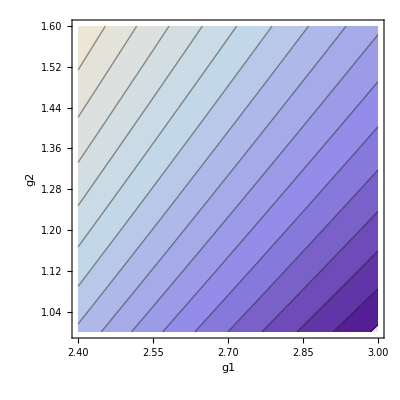

```mathematica
ListContourPlot[Flatten[sol,1],Contours->Table[1.2+0.01 i ,{i,1,20}],(*ContourLabels->True,*)Frame->True,FrameLabel->{"g1","g2"}]
```

```mathematica
LSCoupling[J_,L_,Y_Symbol,χ_Symbol]:=Table[Off[ClebschGordan::phy];{mJ,Sum[Y[L,mL]χ[mS]ClebschGordan[{L,mL},{1/2,mS},{J,mJ}],{mL,-L,L,1},{mS,-1/2,1/2,1}]},{mJ,-J,J,1}]
```

```mathematica
LSCoupling[1/2,1,A,B]//TableForm
```

-1/2 | (A[1,0] B[-1/2])/(√3)-√(2/3) A[1,-1] B[1/2]
1/2 | √(2/3) A[1,1] B[-1/2]-(A[1,0] B[1/2])/(√3)